# approach 1

```mathematica
ClearAll["Global`*"]
```

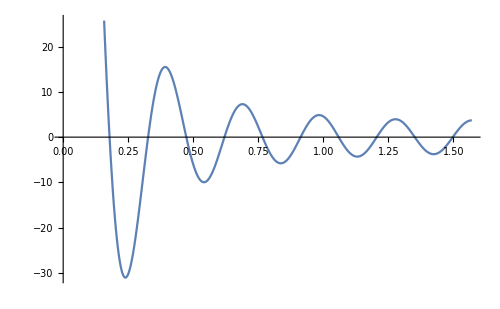

```mathematica
Plot[GegenbauerC[20,3/2,Cos[x]],{x,0,π/2}]
```

```mathematica
FindMinimum[{GegenbauerC[20,3/2,Cos[x]],x>0,x<1},{x,.001}]
```

{-30.9971,{x→0.239191}}

```mathematica
f=246/0.23919130178416434;
f=.
```

```mathematica
Moments[c_,f_]:=Module[{},
Vtree[Π_]:=c GegenbauerC[20,3/2,Cos[Π/f]];
MHiggs[Π_]:=Evaluate[D[Vtree[Π],{Π,2}]];
MGB[Π_]:=Cot[Π/f]D[Vtree[Π],{Π,1}]/f;V1loop[Π_]:=Vtree[Π]+1/64/π^2MHiggs[Π]^2 (Log[MHiggs[Π]/f^2]-1/2)+1/64/π^2MGB[Π]^2 (Log[MGB[Π]/f^2]-1/2);
eq1=D[V1loop[Π],{Π,1}]/.{Π->246};
eq2=D[V1loop[Π],{Π,2}]/.{Π->246};
Return[Re[{eq1,eq2}]]]
```

```mathematica
Moments[400.,1000]
```

{37.1642,5.20051}

# approach 2

```mathematica
ClearAll["Global`*"]
```

```mathematica
Plot[GegenbauerC[20,3/2,Cos[x]],{x,0,π/2}]
```

-Graphics-

```mathematica
FindMinimum[{GegenbauerC[20,3/2,Cos[x]],x>0,x<1},{x,.001}]
```

{-30.9971,{x→0.239191}}

```mathematica
f=246/0.23919130178416434;
Vtree[Π_]:=c GegenbauerC[20,3/2,Cos[Π/f]];
eq2=D[Vtree[Π],{Π,2}]/.{Π->246};
csol=NSolve[{eq2==125^2},c];
c=c/.csol[[1]];
```

```mathematica
{f,c}
```

{1028.47,1.1591×10^6}

```mathematica
MHiggs[Π_]:=Evaluate[D[Vtree[Π],{Π,2}]];
MGB[Π_]:=Evaluate[Cot[Π/f]D[Vtree[Π],{Π,1}]/f];
V1loop[Π_]:=1/64/π^2MHiggs[Π]^2 (Log[MHiggs[Π]/f^2]-1/2)+1/64/π^2MGB[Π]^2 (Log[MGB[Π]/f^2]-1/2)
```

```mathematica
VCWtraditional[msq1_,msq2_]:=1/64/π^2msq1^2 (Log[√(msq1^2)/f^2]-1/2)+1/64/π^2msq2^2 (Log[√(msq2^2)/f^2]-1/2);
VCWreal[msq1_,msq2_]:=If[msq1<0,1/64/π^2msq1^2(-1/2),1/64/π^2msq1^2 (Log[msq1/f^2]-1/2)]+If[msq2<0,1/64/π^2msq2^2(-1/2),1/64/π^2msq2^2 (Log[msq2/f^2]-1/2)]
```

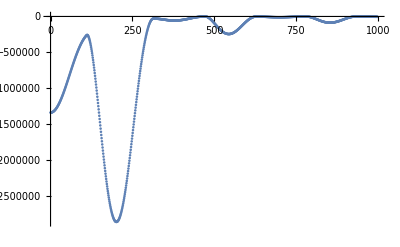

```mathematica
ListPlot[{Table[{Π,VCWreal[MHiggs[Π],MGB[Π]]},{Π,.00001,1000}]}]
```

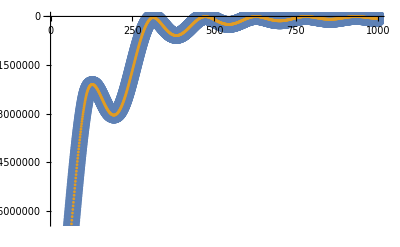

```mathematica
ListPlot[{Table[{Π,Re[V1loop[Π]]},{Π,.00001,1000}],Table[{Π,VCWtraditional[MHiggs[Π],MGB[Π]]},{Π,.00001,1000}]},PlotStyle->{PointSize[.03],PointSize[.005]}]
```

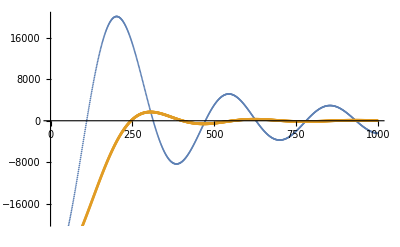

```mathematica
ListPlot[{Table[{Π,MHiggs[Π]},{Π,.00001,1000}],Table[{Π,MGB[Π]},{Π,.00001,1000}]},PlotStyle->{PointSize[.003],PointSize[.005]}]
```

```mathematica
V0full[h_?NumericQ]:=Vtree[h]+VCWreal[MHiggs[h],MGB[h]]
```

```mathematica
(D[V0full[h],{h,1}]/.{h->246.})^(1/3)
```

33.9044

```mathematica
Plot[{Vtree[h],V0full[h]},{h,0,1000},PlotLabels->{"Tree","1-loop"}]
```

-Graphics-